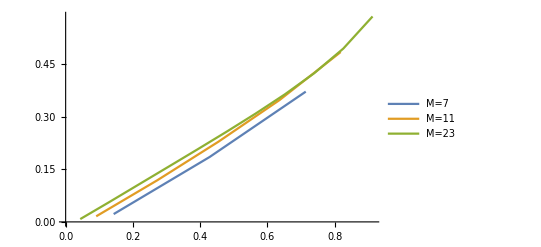

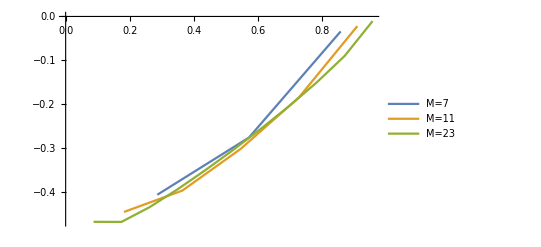

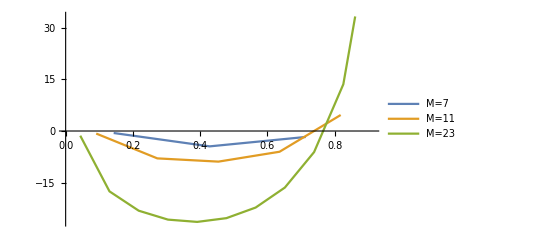

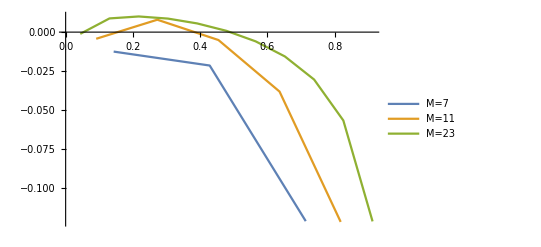

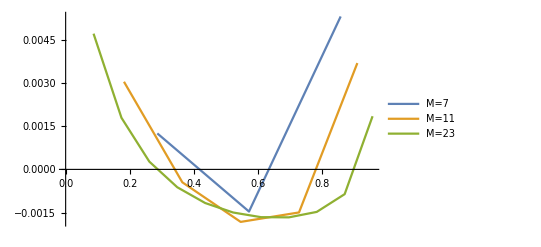

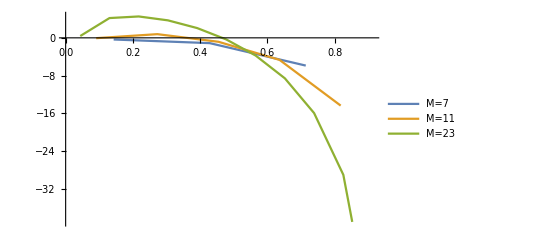

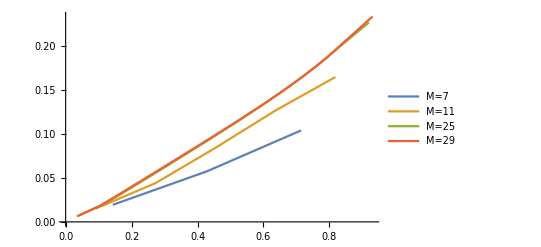

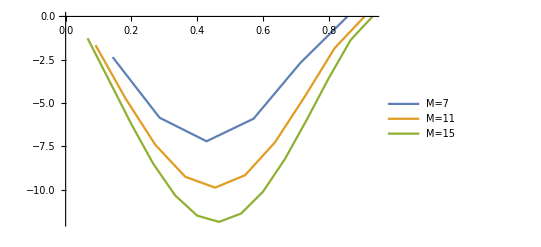

```mathematica
(* notebook to manipulate the stringbit numerical results. *)

ClearAll[ResultFolder,LoadEnergyData];
ResultFolder = NotebookDirectory[]<>"../results/";

(*DataSet: 0 for all data point, 1 for odd only, 2 for even only, 3 for data[L] + data[M-L] *)
Options[LoadEnergyData]={Xi->0,DataSet->0,NormalizeFactorM->0};
LoadEnergyData[s_,M_,opts:OptionsPattern[]]:=Module[{file,data,xi,dataType, ret, len,normpower},
xi = OptionValue[Xi];
file = "s="<>ToString[s]<>"-M="<>ToString[M];
If[xi≠0, file = file <> "-xi="<>ToString[xi]];
data=Import[ResultFolder<>file<>".txt","Table"];

normpower = OptionValue[NormalizeFactorM];
data=data[[2;;Length[data],{2,3}]];
Do[data[[i,1]]=N[data[[i,1]]/M];data[[i,2]]=N[data[[i,2]]/(M^normpower)], {i,1,Length[data]}];

dataType = OptionValue[DataSet];
If[dataType == 0,  Return[data]];
len = Length[data];

If[dataType == 3,
Return[Table[{data[[2i-1,1]], data[[2i-1,2]]+data[[len-2i+2,2]]},{i,1,Round[len/2]}]]
];

If[dataType == 1, 
Return[Table[data[[2*i-1]],{i,1,Floor[(len+1)/2]}]]
];

If[dataType == 2,
Return[Table[data[[2*i]],{i,1,Floor[len/2]}]]
];
];

PlotEnergyCorrection[s_,Mlist_,opts:OptionsPattern[]]:=Module[{data={},labels={},i,toPlot,m},
For[i=1,i≤ Length[Mlist],i++,
m = Mlist[[i]];
toPlot=LoadEnergyData[s,m, FilterRules[{opts},Options[LoadEnergyData]]];
AppendTo[data,toPlot];
AppendTo[labels, "M="<>ToString[m]];
];

ListPlot[data,Join[{PlotLegends->labels},FilterRules[{opts},Options[ListPlot]]]]
];

PlotEnergyCorrection[1,{7,11,23}, Xi->-1,DataSet->1,NormalizeFactorM->2,Joined->True]
PlotEnergyCorrection[1,{7,11,23}, Xi->-1,DataSet->2,NormalizeFactorM->2,Joined->True]
PlotEnergyCorrection[1,{7,11,23}, Xi->-1,DataSet->3,NormalizeFactorM->0,Joined->True]

PlotEnergyCorrection[1,{7,11,23}, Xi->1,DataSet->1,NormalizeFactorM->2,Joined->True]
PlotEnergyCorrection[1,{7,11,23}, Xi->1,DataSet->2,NormalizeFactorM->2,Joined->True]
PlotEnergyCorrection[1,{7,11,23}, Xi->1,DataSet->3,NormalizeFactorM->0,Joined->True]

PlotEnergyCorrection[1,{7,11,25,29}, DataSet->3,NormalizeFactorM->2,Joined->True]
PlotEnergyCorrection[2,{7,11,15}, DataSet->0,NormalizeFactorM->3,Joined->True]
```